Possible implementations of network evolution

```mathematica
vi = {vix,viy,0};
via = {vax,vay,0};
vib = {vbx,vby,0};

A = Sqrt[Cross[via,vi].Cross[via,vi]]+Sqrt[Cross[vi,vib].Cross[vi,vib]]+Sqrt[Cross[vib,via].Cross[vib,via]];
ria = vi - via;
rib = vib - vi;
riba =  Sqrt[rib.rib];
riaa = Sqrt[ria.ria];
P =riaa+riba+Sqrt[(rib+ria).(rib+ria)];
En = K/2*(A-a)^2+G/2*P^2+L*(Sqrt[ria.ria]+Sqrt[rib.rib]);

F = -{D[En,vix],D[En,viy]}/. A -> An/.P -> Pn/.(-vay vix+vax viy)/(√(-vay vix+vax viy)^2)-> 1/. (vby vix-vbx viy)/(√(vby vix-vbx viy)^2)-> 1/.1/(√((vbx-vix)^2+(vby-viy)^2))->1/rbi/.1/(√((-vax+vix)^2+(-vay+viy)^2))-> 1/rai;
F/.(vbx-vix)/rbi-> nibx/.(-vax+vix)/rai->- niax/.(vby-viy)/rbi-> niby/.(-vay+viy)/rai->- niay/.K->0
```

{-L (-niax-nibx)-G (-niax-nibx) Pn,-L (-niay-niby)-G (-niay-niby) Pn}

```mathematica
z = {0,0,1};
nA = Cross[z,via-vib]
```

{-vay+vby,vax-vbx,0}

```mathematica
Endev = En/.vix-> vix+dx/.viy-> viy+dy;
```

Now we will consider a set of coefficients and parameters to get the force acting on a vertex on a square.

```mathematica
vu = {-2.5,2.5,0};
va = {2.5,2.5,0};
vb = {-2.5, -2.5,0};
zunit= {0,0,1};

A = 25;
P = 20;
K = 0.006;
A0 = Pi*(5/3)^2;
G = 1;
L = -1;

nA = Cross[ zunit,va-vb];
rua = vu - va;
rbu = vb-vu;
nua = rua/Sqrt[rua.rua];
nbu = rbu/Sqrt[rbu.rbu];
nP = nua-nbu;

F = -K/2*(A-A0)*nA-(G*P+L/2)*nP
```

{19.7441,-19.7441,0.}

```mathematica
{2.5,2.5,0}
```

{2.5,2.5,0}

Exploring the adjacency and Laplace matrices of a graph undergoing a rearrangement

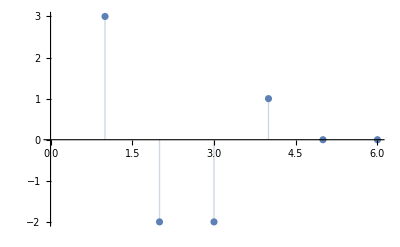

```mathematica
G1 = UndirectedGraph[{1-> 2,1-> 4,1-> 3,2-> 5,2-> 6,4->3,3 -> 6, 6-> 5,5-> 4}];
A1 = AdjacencyMatrix[G1];
Eigenvalues[A1];


G2 = UndirectedGraph[{1-> 2,1-> 4,1-> 5,2-> 3,2-> 6,4->3,3 -> 6, 6-> 5,5-> 4}];
A2 = AdjacencyMatrix[G2];
ListPlot[Eigenvalues[A2],Filling->Axis]
```

This expression is the energy for the minimal wound area after a change of variable a to ar = a^(1/2). It turns this root polynomial into a cubic polynomial that can be more readily solved

```mathematica
Clear[aa,bb,dEda];
aa[l_,n_,r_]:=Sqrt[r]/(l*(n)) + 1/(4*n) ;
bb[l_,n_,r_,b_] = Sqrt[r]*(1/(l*(n)) +1/(2*b*r))+ 1/(4*n) - 1/2;
dEda[ar_, b_, l_, n_,r_] := (aa[l,n,r]*ar^2 - bb[l,n,r,b])*ar^(1) -1
```

```mathematica
nInput =25;
rho = 1/(4*Pi);
List1 = {0.655,0.677,0.699,0.703,0.708,0.712,0.714,0.7151,0.7153,0.716,0.721,0.725,0.730,0.734,0.738,0.743};
List2 = {3.04,2.72,2.11,1.91,1.66,1.34,1.15,1.093,1.090,1.075,1.039,1.019,1.007,1.002,1.001,1.000};
```

```mathematica
rho
```

1/(4 π)

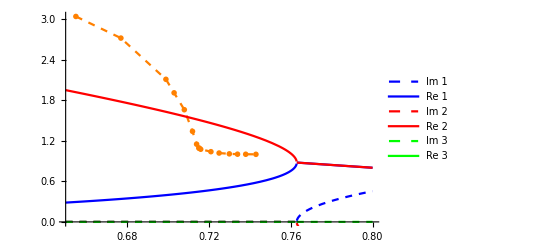

```mathematica
r = Solve[dEda[a,2*b,100*b/300,nInput,rho]== 0,a];
r1 = r[[1]][[1]];
s1 = a/.r1;
ss1 =s1^2/0.2;

r2 = r[[2]][[1]];
s2 = a/.r2;
ss2 = s2^2/0.2;

r3 = r[[3]][[1]];
s3 = a/.r3;
ss3 = s3^2/0.2;

data  = Transpose@{List1,List2};

p1 = Plot[{Im[ss3/nInput],Re[ss3/nInput],Im[ss2/nInput],Re[ss2/nInput],Im[ss1/nInput],Re[ss1/nInput]},{b,0.65,0.80},PlotStyle-> {{Blue,Dashed},Blue,{Red, Dashed},Red,{Green,Dashed},Green}, PlotLegends->{HoldForm["Im 1"],HoldForm["Re 1"],HoldForm["Im 2"],HoldForm["Re 2"],HoldForm["Im 3"],HoldForm["Re 3"]}];
p2 = ListPlot[data,Joined->True, PlotMarkers-> {-Graphics-, Medium},PlotStyle->{{Orange,Dashed}}, PlotRange->{{0.65,0.8},Automatic}];
Show[p2,p1]
```

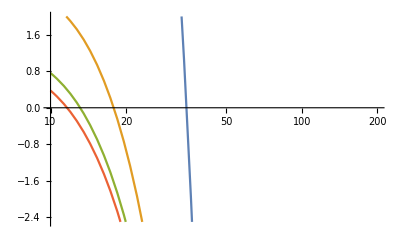

```mathematica
LogLinearPlot[{dEda[ar^0.5,0.2,2.4*0.2,nInput,rho],dEda[ar^0.5,0.6,2.4*0.6,nInput,rho],dEda[ar^0.5,0.75,2.4*0.75,nInput,rho],dEda[ar^0.5,0.8,2.4*0.8,nInput,rho]},{ar,10,200},PlotRange->{-2.5,2}]
```

```mathematica
(List2[[1]]*0.462)^(0.5)
```

1.18511

```mathematica
R = Solve[dEda[(List2[[1]]/0.462)^(0.5),List1[[1]],2.28*List1[[1]],nFit,rho]==0, nFit];
R
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
E1 = 1/(2*(n-1))*(1-a)^2;
E2 = la/(2*b*r)*((Sqrt[n-a]-Sqrt[r(n-1)]*b))^2;
E3 = 2*la*Sqrt[a/r];
dE = D[E1,a]+D[E2,a]+D[E3,a]
```

-(1-a)/(-1+n)+la/(√(a/r) r)-(la (√(-a+n)-b √((-1+n) r)))/(2 b √(-a+n) r)

```mathematica
Serie1 = Series[-(1-a)/(-1+1/x)+la/(√(a/r) r)-(la (√(-a+1/x)-b √((-1+1/x) r)))/(2 b √(-a+1/x) r),{x,0,1}];
Normal[Serie1];
lindE = a^(1/2)*Expand[Normal[Serie1]]/.x-> 1/n
```

√a (-1/n+a/n+(la √(a/r))/a-la/(2 b r)-(la √(n r))/(4 n^(3/2) r)+(a la √(n r))/(4 n^(3/2) r)+(la √(n r))/(2 √n r))

```mathematica
SimpleSolver = Numerator[PowerExpand[Simplify[lindE],a]]
```

(4 √a b la n^(3/2))/(√(1/r))+a^2 b (4 √n r+la √(n r))-a (4 b √n r+la (2 n^(3/2)+b √(n r)-2 b n √(n r)))

```mathematica
Manipulate[Plot[(SimpleSolver/.n-> 13)/.r-> 1/(4Pi)/. la -> b*2.28,{a,-100,100}],{b,-20,20}]
```

```mathematica
R = Solve[(SimpleSolver/.la-> b*2.28/.n-> 25/.r-> 1/(4Pi)) == 0,a];
R2= a/.R[[2]][[1]];
R3 = a/.R[[3]][[1]];
R4 = a/.R[[4]][[1]];
```

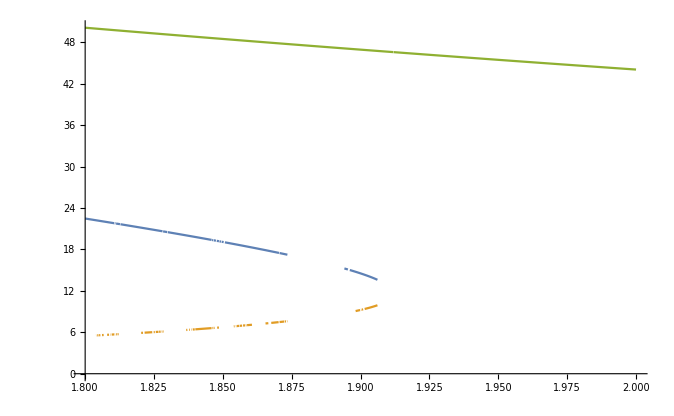

```mathematica
Plot[{R2,R3,R4},{b,1.8,2}]
```

```mathematica
Collect[Expand[lindE*Sqrt[r]/la],a]
```

(√(a/r) √r)/(√a)+a^(3/2) ((√r)/(la n)+(√(n r))/(4 n^(3/2) √r))+√a (-1/(2 b √r)-(√r)/(la n)-(√(n r))/(4 n^(3/2) √r)+(√(n r))/(2 √n √r))

```mathematica
Im[ss3/nInput]/.b-> 0.71225
```

0.00865737

```mathematica
rho
```

1/(8 √3)

```mathematica
(1/2-1/100)/((3/25+Sqrt[3]/32)*Sqrt[8*Sqrt[3]])
```

49/(200 √2 3^(1/4) (3/25+(√3)/32))

```mathematica
N[49/(200 √2 3^(1/4) (3/25+(√3)/32))]
```

0.755972

```mathematica
((1/(2 √2 3^(1/4) (3/23+(√3)/32)))*(√(1/(8 √3)))-(√3)/32)*25
```

25 (-(√3)/32+1/(8 √3 (3/23+(√3)/32)))

```mathematica
N[25 (-(√3)/32+1/(8 √3 (x/25+(√3)/32)))]
```

```mathematica
-(√3)/32+1/(8 √3 (x/25+(√3)/32))
```

```mathematica
25(-(√3)/32+1/(8 √3 ((√3)/32+x/25)))
```

25 (-(√3)/32+1/(8 √3 ((√3)/32+x/25)))

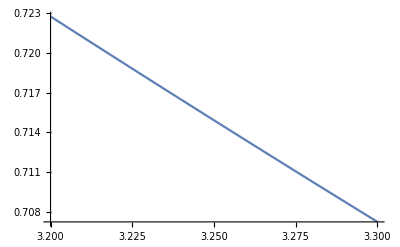

```mathematica
Plot[ 49/(200 √2 3^(1/4) (x/25+(√3)/32)),{x,3.2,3.3}]
```

```mathematica
RootReduce[49/(200 √2 3^(1/4) (8.42255/25+(√3)/32))]
```

0.336637

```mathematica
N[Root[-103246571305024+168266689920000 #1^2+68205048046875 #1^4&,2,0]]
```

0.713231

```mathematica
N[Root[-312299584+508953600 #1^2+161670843 #1^4&,2,0]]
```

0.725116

```mathematica
N[Root[-286557184+487526400 #1^2+161670843 #1^4&,2,0]]
```

0.709688

```mathematica
N[Root[-368947264+553190400 #1^2+161670843 #1^4&,2,0]]
```

0.755972

```mathematica
NCrit[b_] =  49/4*√(8 √3)*b-50 √3
```

-50 √3+(49 3^(1/4) b)/(√2)

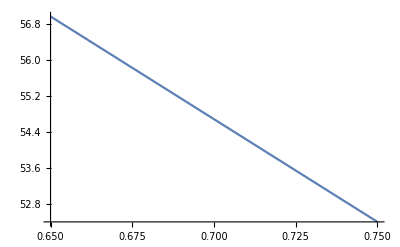

```mathematica
Plot[50 √3-(49 3^(1/4) b)/(√2),{b,0.65,0.75}]
```